```mathematica
PrependTo[$Path,"/home/cookgb/Research/KerrQNM/KerrModes"];
Needs["KerrTTML`"]
SetSpinWeight[-2]
```

All KerrMode routines (TTML) set for Spin-Weight s = -2

```mathematica
SchTTMLTable[2]=2;
SchTTMLTable[2,0]={0.37-0.09*I,0,0,0,0};
SchTTMLTable[2,0]={0.007-2.009*I,0,0,0,0};
SchTTMLTable[2,1]={0.35-0.27*I,0,0,0,0};
SchTTMLTable[3]=2;
SchTTMLTable[3,0]={0.6-0.09*I,0,0,0,0};
SchTTMLTable[3,1]={0.6-0.28*I,0,0,0,0};
```

```mathematica
$MinPrecision=24
```

24

```mathematica
Plot3D[Abs[PlotContFrac[0,-2,-1,1/2,4,ωr-ⅈ ωi,300,15]],{ωr,0,10},{ωi,0,10}]
```

-Graphics3D-

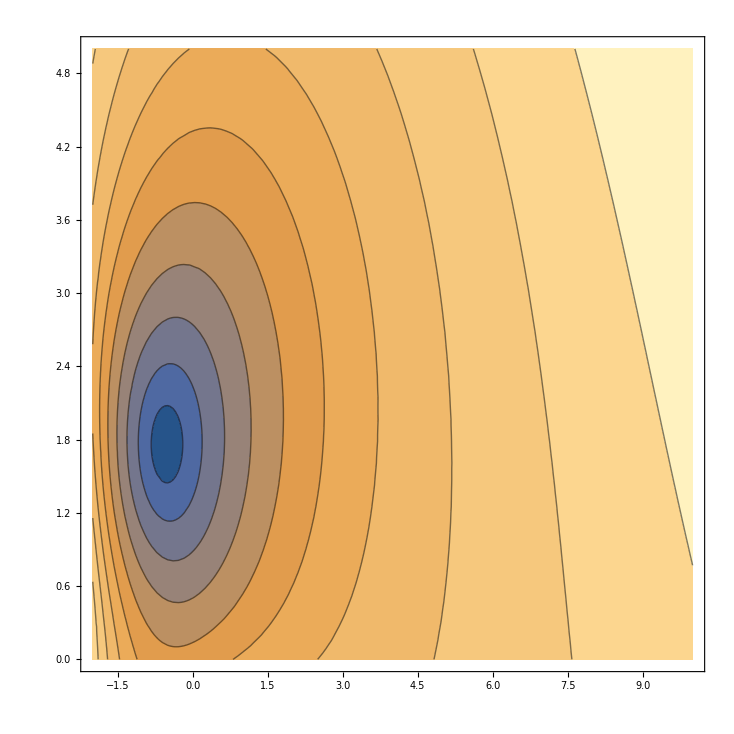

```mathematica
ContourPlot[Abs[PlotContFrac2[0,-2,-2,1/8,1,ωr-ⅈ ωi,300,15]],{ωr,-2,10},{ωi,0,5},Contours->10]
```

```mathematica
Plot3D[{Re[PlotContFrac2[0,-2,-1,1/2,1,ωr-ⅈ ωi,3000,15]],Im[PlotContFrac2[0,-2,-1,1/2,1,ωr-ⅈ ωi,3000,15]]},{ωr,0,5},{ωi,0,5}]
```

-Graphics3D-

```mathematica
Plot3D[{Re[RadialCFRem[0,-2,0,0,4,ωr-ⅈ ωi,300][[1]]],Im[RadialCFRem[0,-2,0,0,4,ωr-ⅈ ωi,300][[1]]]},{ωr,0,4},{ωi,0,4}]
```

-Graphics3D-

```mathematica
RadialCFRem[0,-2,0,0,10,-ⅈ 10,2]
```

{0,2}

```mathematica
SchwarzschildTTML[2,0,RadialDebug->1,SchDebug->0]
```

Computing (l=2,n=0)

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

δω= 0 root= 0.

Det::mindet: Input matrix contains an indeterminate entry.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

δω= 0 root= 0.

Warning: resetting newNrcf = 300

{0.-2. ⅈ,0,300,-14,0}

```mathematica
?SchwarzschildTTML
```

SchwarzschildTTML[l,n] computes the Quasi-Normal Mode solutions for overtone n of mode l.  The mode is computed to an accuracy of 10^-14.  For given 'l', if solutions with overtones (n-1) and (n-2) have not been computed, then the routine is recersively called for overtone '(n-1).  If no solutions exist for mode l, then the first two overtones of (l-1) and (l-2) are used to extrapolate initial guesses for these modes.

Options:
	 SpinWeight→Null : -2,-1,0
		 The spin weight must be set via a call to SetSpinWeight before any KerrTTML
		 function call.
	 ModePrecision→24
	 JacobianStep→-10
		 The radial solver make use of numerical derivatives.  The relative step size
		 is set to 10^JacobianStep.
	 RadialCFMinDepth→300
		 The minimum value for the Radial Continued Fraction Depth.
	 RadialCFDepth→1
		 The initial Radial Continued Fraction Depth is usually taken from the prior 
		 solution in the sequence.  Fractional values reduce this initial value by that
		 fraction.  Integer values larger than RadialCFMinDepth are used as the new
		  initial value.
	 RadialRelax→1
		 Initial under-relaxation parameter used in Radial Newton iterations.
	 Rootϵ→-14
		 10^Rootϵ is the maximum allowed magnitude for the Radial Continued Fraction.
	 SchDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Schwarzschile iterations.
	 RadialDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Radial Newton iterations.